# Ping Pong Juggler - Dynamic Analysis Ball falling on tilted flat surface

```mathematica
Quit[]
```

-Tan[(7 π)/36]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x'[tp]→2.03423×10^-16,y'[tp]→-7.24562,λ→9.57575×10^-19},{x'[tp]→6.80866,y'[tp]→2.47815,λ→0.0320504}}

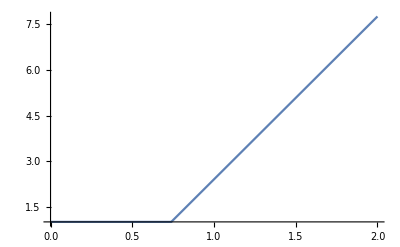

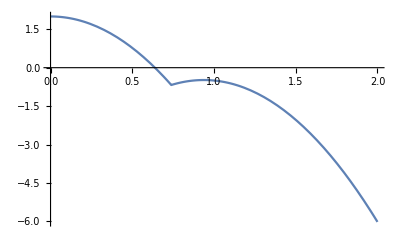

```mathematica
(* Dimensions and Parameters *)
θ=-35;
θ=θ*Pi/180;
r=.02; (* The ball's diameter is 40 mm *)
l=.17; (* the length of the paddle is 17 cm *)
m=.0027; (* mass of the ball is 2.7 grams *)
g=9.81;

(* Bouncing parameters *)
(* The ping pong rules say that the ball should bounce up 24-26 cm when dropped from a height of 30.5 cm onto a steel block (with a coefficient of restitution of .89 to .92). *)
bouncePerc=24/30.5;
 
(* States *)
q={{x[t],y[t]}};
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
T=0.5*m*dq.dqᵀ;
V=m*g*q[[1,2]];
L=T-V;

(* Euler Lagrange eq's *)
EL=(D[D[L,dq],t]-D[L,q])[[1,1]];

(* Solve *)
temp=Solve[EL[[1]]==0&&EL[[2]]==0,ddq[[1]]];
eq1=ddq[[1,1]]==temp[[1,1,2]];
eq2=ddq[[1,2]]==temp[[1,2,2]];

(* Conditions *)
initCond={x[0]==1,y[0]==2,x'[0]==0,y'[0]==0};

(* Impact *)
m=Tan[θ]
ϕ=(-m*x[t]+y[t])/Sqrt[m^2+1] - r;

(* NDSolve *)
sol=NDSolve[Join[{eq1,eq2},initCond],{x,y},{t,0,2},Method->{"EventLocator","Event"->ϕ,"EventAction":>Throw[τ=t,"StopIntegration"]}];

(* Impact Update *)
P=D[L,dq];
H=P.dq[[1]]-L;
Hplus=((H/.t->tp)/.{x[tp]->(x[τ]/.sol)[[1]],y[tp]->(y[τ]/.sol)[[1]]})[[1,1]];
Hminus=((H/.t->τ)/.sol)[[1]][[1,1]];
Pplus=((P/.t->tp)/.{x[tp]->(x[τ]/.sol)[[1]],y[tp]->(y[tp]/.sol)[[1]]})[[1]];
Pminus=(((P/.t->τ)/.sol)[[1]])[[1]];
gradphi=D[ϕ,q];
gradphi={((gradphi/.t->τ)/.sol)[[1]]};
Himp=Hplus-Hminus==0;
Pimp=Pplus-Pminus==λ*gradphi;
qpupdate=Solve[{Hplus-Hminus==0,Pplus-Pminus==λ*gradphi},{x'[tp],y'[tp],λ}]

(* New Conditions *)
initCond={x[τ]==(x[τ]/.sol)[[1]],y[τ]==(y[τ]/.sol)[[1]],x'[τ]==bouncePerc*(x'[tp]/.qpupdate[[2]]),y'[τ]==bouncePerc*(y'[tp]/.qpupdate[[2]])};

(* More NDSolve *)
sol2=NDSolve[Join[{eq1,eq2},initCond],{x,y},{t,τ,2}];

(* Plots *)
xsol1=x[t]/.sol[[1]];
xsol2=x[t]/.sol2[[1]];
xsol=Piecewise[{{xsol1,t<τ},{xsol2,t≥τ}}];
ysol1=y[t]/.sol[[1]];
ysol2=y[t]/.sol2[[1]];
ysol=Piecewise[{{ysol1,t<τ},{ysol2,t≥τ}}];

Plot[xsol,{t,0,2}]
Plot[ysol,{t,0,2}]

X[τ_]:=xsol/.t->τ;
Y[τ_]:=ysol/.t->τ;

Animate[Graphics[{PointSize[r],Point[{X[tt],Y[tt]}],Line[{{0,0},{2*Cos[θ],2*Sin[θ]}}]},Axes->True,PlotRange->{{-.5,10},{-5,2}}],{tt,0,2}]
```